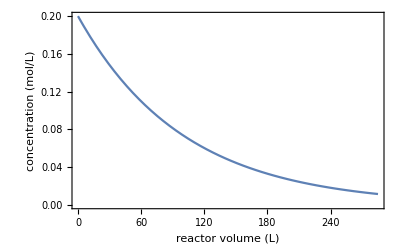

```mathematica
Module[{k,vo,Vf,Cao,Ca,sol},
k=0.5;(*1/s*)
vo=50;(*L/s*)
Vf=285;(*L*)
Cao=0.2;(*mol/L*)

Ca[V_]=Fa[V]/vo;

sol=NDSolve[
{Fa'[V]==-k*Ca[V],
Fa[0]==vo*Cao},
Fa,
{V,0,Vf}];

Plot[Ca[V]/.sol,{V,0,Vf},
Frame->True,
FrameLabel->{"reactor volume (L)","concentration (mol/L)"},
LabelStyle->{16,Black}]
]
```

```mathematica
(*differential equations*)
ode={
	f'[x]==f0*(1-f[x]),
	g'[x]==g0
	};
(*initial/boundary conditions*)
conditions={
	f[0]==f0,
	g[0]==g0
	};
(*variables you're solving for*)
variables={f,g};

sol=NDSolve[{ode,conditions},variables,{x,0,xf}];

Plot[{f[x]/.sol, g[x]/.sol},{x,0,xf}]
```